## Legend for coloring

Flow of the discussion and labels for the action being performed.

Technical comments (mostly on the Mathematica commands).

Comments and thoughts on what we are seeing.

## Technical Setup

Define some system-specific variables here - e.g. the base path for where the data files are stored. For some reason, Mathematica does not import the file successfully if it’s just located in the same folder and the path is omitted.

```mathematica
pathBase="/Users/ivanevtimov/GDrive-Laf/THESIS/Results with more subjects/";
```

Import the data. Caution! This takes a while as the file is ~300MB.

```mathematica
data=Import["allcodes_data.csv",Path->pathBase,HeaderLines->1];
```

Define function functions for accessing the data.

```mathematica
meb[i_]:=data[[i,4;;259]];
subject[i_]:=data[[i,1]];
imgcode[i_]:=data[[i,2]];
isFA[r_]:=r[[2]]=="fa";
isFB[r_]:=r[[2]]=="fb";
isRC[r_]:=r[[2]]=="rc";
isTrue[r_]:=r[[2]]=="true";
```

Generate the mean (average) of each neuron’s activation.

```mathematica
meanFAs=Table[Mean[Select[data,isFA][[All,i]]],{i,4,259}];
```

```mathematica
meanFBs=Table[Mean[Select[data,isFB][[All,i]]],{i,4,259}];
```

```mathematica
meanRCs=Table[Mean[Select[data,isRC][[All,i]]],{i,4,259}];
```

```mathematica
meanTrue=Table[Mean[Select[data,isTrue][[All,i]]],{i,4,259}];
```

Function to create a list of (x,y) pairs where x is the index of the neuron and y is its activation value.

```mathematica
indexate[l_]:=Table[{i,l[[i]]},{i,1,Length[l]}]
```

## Graphs

### Average over All the Subjects

This graph shows the difference between the mean activations across all subjects and the mean of the ground truth (again, across all subjects). 

A better way to explain this is to imagine this process:
1. For each given neuron: find the mean activation value across all subjects for a particular image type and for the ground truth.
2. Find the difference between the mean value of the ground truth and the mean activation value (for the respective image type).
3. For each neuron, graph a point indicating this difference.

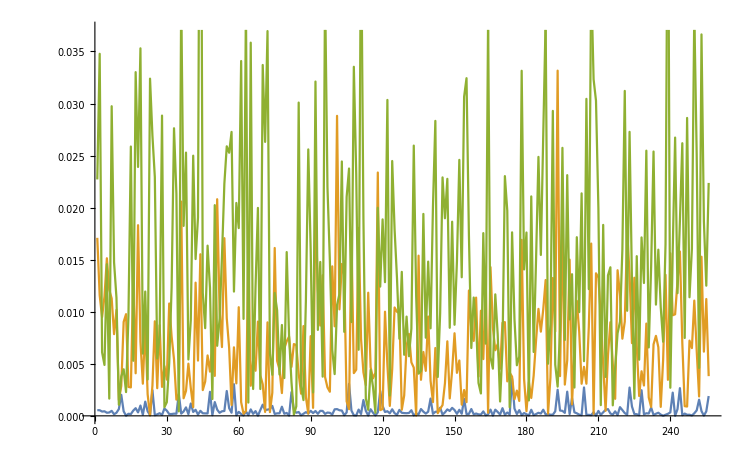

```mathematica
ListLinePlot[indexate/@Abs/@{(meanTrue-meanFAs),(meanTrue-meanFBs),(meanRCs-meanTrue)},AxesOrigin->{0,0}]
```

Comment: Arguably, we are losing a lot of information by averaging out over all subjects. However, some things are clear already. 
1) The difference between the FA’s activations and the ground truth is mostly bounded to <0.001 and definitely by <0.005. So the network is learning the FA’s really well.
2) The FB’s are mostly within 0.015 and some spike up to a difference of 0.030. Again, we are losing a lot of information by averaging out across all subjects. Yet it is clear that the FB’s are further away from the truth than the FA’s.
3) The same can be said for the RC’s -- they are even farther away.

Let’s say we wanted to find out which neuron changes the most from between the RC and the FB activations. This graph could show us just that. 

It plots the difference between the mean FB activation value and the mean RC activation value when the mean is taken across all variations of all subjects.

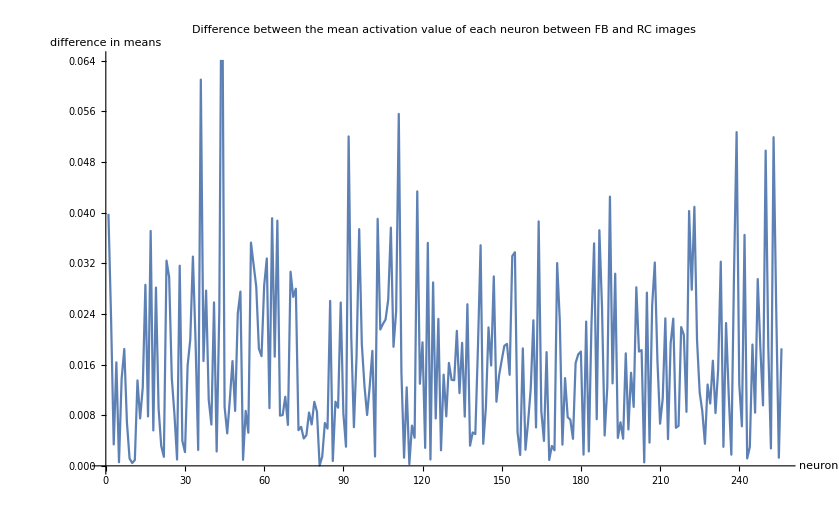

```mathematica
Show[ListLinePlot[indexate/@Abs/@{(meanFBs-meanRCs)},AxesOrigin->{0,0}],AxesLabel->{HoldForm[neuron],HoldForm[difference in means]},PlotLabel->HoldForm[Difference between the mean activation value of each neuron between FB and RC images],LabelStyle->{GrayLevel[0]}]
```

Comment: We are definitely losing information by averaging out everything, yet judging by this graph, the distances do not seem significant.
It would be interesting to:
1) divide by the standard deviation to standardize these differences (or another appropriate statistical technique) 
2) look at a similar plot for one subject only
in order to gain more information

### Focus on Subject 00070

Subject 00070 is interesting because the evaluation achieved 0 matching scores both for the RC’s and for the FB’s. So what went wrong?

First, a quick function that we will use in the selection.

```mathematica
isSubj70[r_]:=r[[1]]==70;
```

```mathematica
dataSubj70=Select[data, isSubj70];
```

```mathematica
subj70True=Select[dataSubj70,isTrue][[1,4;;259]];
meanFA70=Table[Mean[Select[dataSubj70,isFA][[All,i]]],{i,4,259}];
meanFB70=Table[Mean[Select[dataSubj70,isFB][[All,i]]],{i,4,259}];
meanRC70=Table[Mean[Select[dataSubj70,isRC][[All,i]]],{i,4,259}];
```

Let us first plot the (absolute) difference between the real MEB code for subject 70 and the activation values for each neuron for FA, FB, and RC images, respectively.

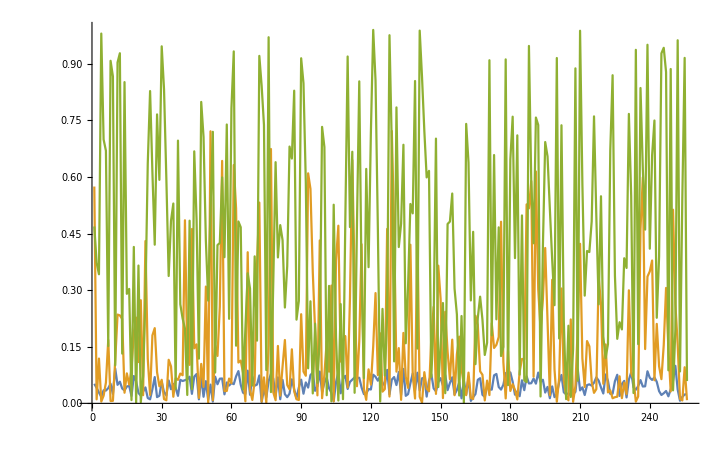

```mathematica
ListLinePlot[indexate/@Abs/@{(subj70True-meanFA70),(subj70True-meanFB70),(subj70True-meanRC70)},AxesOrigin->{0,0}]
```

Comment: Wow. The RC’s are very far off -- with wild variations. Whereas the FA’s are all in a band around 0.02 (we trained on them after all), the FB’s and the RC’s vary wildly. There are many neurons where the RC is not only not close but the exact opposite of what the real MEB is.

Let us now look at the difference between the FB and the RC.

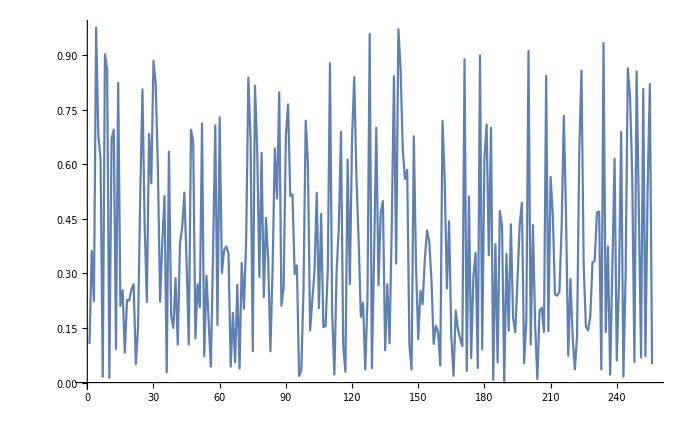

```mathematica
ListLinePlot[indexate/@Abs/@{(meanFB70-meanRC70)},AxesOrigin->{0,0}]
```

Comment: On first glance, it seems like we have a problem -- many neurons shift completely when moving from an RC to an FB. However, I would not jump to that conclusion yet as it seems like the RC is just random noise.

### Focus on Subject ??????

Subject ????? is interesting because the evaluation achieved a really good score on the FB’s but a very low score on the RC’s. So what went wrong when we moved from the FB’s to the RC’s?